# Calculation of S_2[x]

## Brute force calculation

```mathematica
Λ2=8000;
gn=Table[{n,SquaresR[2,n]},{n,0,Λ2}];
```

```mathematica
gn[[1;;10]]
```

{{0,1},{1,4},{2,4},{3,0},{4,4},{5,8},{6,0},{7,0},{8,4},{9,4}}

```mathematica
S2[x_,Λ_]:=Sum[gn[[i,2]]/(gn[[i,1]]-x),{i,1,Λ+1}]-π Log[Λ]
```

```mathematica
s2=Table[{x,S2[x,Λ2]},{x,-4,10,.025}];
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

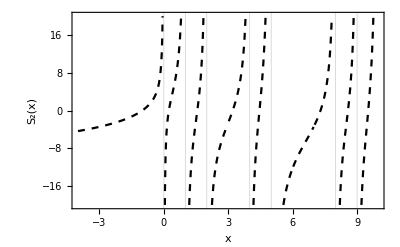

```mathematica
ListPlot[s2,Joined->True,Frame->True,FrameStyle->Directive[Black,14],PlotStyle->{Black,Dashed},GridLines->{{0,1,2,4,5,8,9},None},PlotRange->{All,{-20,20}},FrameLabel->{"x","S_2(x)"}]
```